```mathematica
FNJ=FileNameJoin;
```

```mathematica
RelativeDir[dir_]:=FileNameJoin[{NotebookDirectory[],dir}]
```

```mathematica
Replicate[list_,n_]:=Flatten[Transpose[ConstantArray[list,n]]]
```

```mathematica
ToText[list_]:=StringJoin[Riffle[ToString[#]&/@list,"\n"]]
```

### Before simulation:

```mathematica
(*-------parameters-------*)
td = 8; blocks = 4; l = 100;
(*------------------------*)
data=RandomInteger[{-16,16},l];
ker = RandomInteger[{-16,16},td*blocks];
```

```mathematica
expected=ListConvolve[Reverse[ker],data,{1,-1},0];
```

```mathematica
Max[Abs[expected]]
```

1508

```mathematica
Export[RelativeDir["data.dat"],ToText[Replicate[data,td]]];Export[RelativeDir["coefs.dat"],ToText[ker]];
```

### After simulation:

```mathematica
result=Flatten[Import[RelativeDir[FNJ[{"edit_firIP_v1_0.sim","sim_1","behav","xsim","out.dat"}]]]];
```

```mathematica
SequencePosition[result,Replicate[expected,td]]
```

{}

### Samples from fpga:

```mathematica
2^14
```

16384

```mathematica
85*6229+960
```

530425

```mathematica
snaps=Reverse/@Import[RelativeDir["snap01.dat"]];
registers = {"fir_in","sum_loop_out", "sum_loop_end", "count","x","coef_crr","sum_in","sum_out"}
```

{fir_in,sum_loop_out,sum_loop_end,count,x,coef_crr,sum_in,sum_out}

```mathematica
TableForm[Join[{registers},Transpose@snaps]]
```

fir_in | sum_loop_out | sum_loop_end | count | x | coef_crr | sum_in | sum_out
-87 | 16383 | 3049 | 0 | -87 | 52 | 3049 | -4472
-78 | 16383 | -4428 | 1 | -84 | 6229 | 0 | -543613
-78 | 16383 | -5859 | 0 | -78 | 52 | -5859 | -4160
-80 | 16383 | 1361 | 1 | -83 | 6229 | 0 | -507729
-80 | 0 | -7546 | 0 | -80 | 52 | -7546 | -4524
-89 | 0 | -4527 | 1 | -85 | 6229 | 0 | -529095
-89 | 16383 | -960 | 0 | -89 | 52 | -960 | -4056
-86 | 16383 | -7240 | 1 | -91 | 6229 | 0 | -524553
-86 | 16383 | -5948 | 0 | -86 | 52 | -5948 | -4160
-89 | 16383 | 8058 | 1 | -86 | 6229 | 0 | -530425
-89 | 0 | 1144 | 0 | -89 | 52 | 1144 | -4628
-82 | 0 | 5427 | 1 | -80 | 6229 | 0 | -572787
-82 | 0 | -6615 | 0 | -82 | 52 | -6615 | -4472
-82 | 0 | -896 | 1 | -87 | 6229 | 0 | -534550
-82 | 16383 | -6686 | 0 | -82 | 52 | -6686 | -4628
-89 | 16383 | 3882 | 1 | -78 | 6229 | 0 | -504935
-89 | 0 | -1184 | 0 | -89 | 52 | -1184 | -4264
-78 | 0 | 1884 | 1 | -80 | 6229 | 0 | -548609
-78 | 0 | -4538 | 0 | -78 | 52 | -4538 | -4264
-87 | 0 | -7544 | 1 | -89 | 6229 | 0 | -487046
-87 | 16383 | -7490 | 0 | -87 | 52 | -7490 | -4628
-81 | 16383 | -7723 | 1 | -86 | 6229 | 0 | -502858
-81 | 16383 | -6848 | 0 | -81 | 52 | -6848 | -4056
-84 | 16383 | 2491 | 1 | -89 | 6229 | 0 | -561871
-84 | 0 | -6191 | 0 | -84 | 52 | -6191 | -4524
-76 | 0 | 8089 | 1 | -82 | 6229 | 0 | -542542
-76 | 0 | -7774 | 0 | -76 | 52 | -7774 | -4212
-89 | 0 | -5441 | 1 | -82 | 6229 | 0 | -560572
-89 | 16383 | 5373 | 0 | -89 | 52 | 5373 | -4368
-84 | 16383 | -4519 | 1 | -89 | 6229 | 0 | -518552
-84 | 16383 | 5201 | 0 | -84 | 52 | 5201 | -3952
-86 | 16383 | -4226 | 1 | -78 | 6229 | 0 | -505405
-86 | 16383 | -4947 | 0 | -86 | 52 | -4947 | -4628
-82 | 16383 | -2806 | 1 | -87 | 6229 | 0 | -549180
-82 | 16383 | 6322 | 0 | -82 | 52 | 6322 | -4368
-89 | 16383 | 1589 | 1 | -81 | 6229 | 0 | -490809
-89 | 0 | -7853 | 0 | -89 | 52 | -7853 | -4472
-82 | 0 | -5479 | 1 | -84 | 6229 | 0 | -535601
-82 | 16383 | -2858 | 0 | -82 | 52 | -2858 | -4264
-85 | 16383 | -7594 | 1 | -76 | 6229 | 0 | -512402
-85 | 16383 | -2968 | 0 | -85 | 52 | -2968 | -4628
-84 | 16383 | -4713 | 1 | -89 | 6229 | 0 | -526094
-84 | 16383 | -4217 | 0 | -84 | 52 | -4217 | -4264
-81 | 16383 | 1226 | 1 | -84 | 6229 | 0 | -476372
-81 | 0 | 6948 | 0 | -81 | 52 | 6948 | -4420
-79 | 0 | 7889 | 1 | -86 | 6229 | 0 | -558598
-79 | 0 | -601 | 0 | -79 | 52 | -601 | -4368
-90 | 0 | -2733 | 1 | -82 | 6229 | 0 | -516288
-90 | 16383 | -3807 | 0 | -90 | 52 | -3807 | -4212
-76 | 16383 | 369 | 1 | -89 | 6229 | 0 | -536295
-76 | 0 | 4119 | 0 | -76 | 52 | 4119 | -4108
-85 | 0 | 919 | 1 | -82 | 6229 | 0 | -514585
-85 | 0 | 3147 | 0 | -85 | 52 | 3147 | -4680
-91 | 0 | -925 | 1 | -85 | 6229 | 0 | -550262
-91 | 16383 | 299 | 0 | -91 | 52 | 299 | -3952
-83 | 16383 | -3527 | 1 | -84 | 6229 | 0 | -507631
-83 | 16383 | -2636 | 0 | -83 | 52 | -2636 | -4420
-91 | 16383 | -5246 | 1 | -81 | 6229 | 0 | -529166
-91 | 16383 | 1632 | 0 | -91 | 52 | 1632 | -4732
-87 | 16383 | -3700 | 1 | -79 | 6229 | 0 | -525872
-87 | 16383 | -8151 | 0 | -87 | 52 | -8151 | -4316
-86 | 16383 | 2304 | 1 | -90 | 6229 | 0 | -502917
-86 | 0 | -7868 | 0 | -86 | 52 | -7868 | -4732
-83 | 0 | -3817 | 1 | -76 | 6229 | 0 | -500242

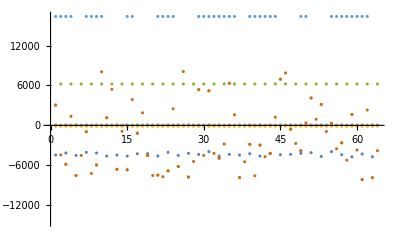

```mathematica
ListPlot[Reverse[snaps]]
```

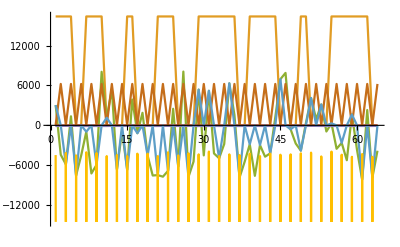
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[snaps,Joined->True]&/@snaps
```

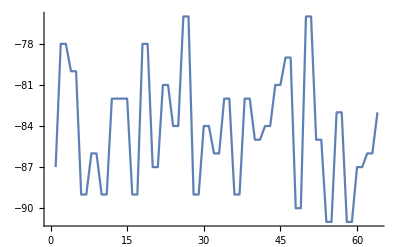

```mathematica
ListPlot[snaps[[1]],Joined->True]
```